# R-ratio computation

```mathematica
description="Ga^* -> Q Qbar, NLO QCD, R-ratio";
```

## Resources

```mathematica
Quit[]
```

```mathematica
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Real-emission

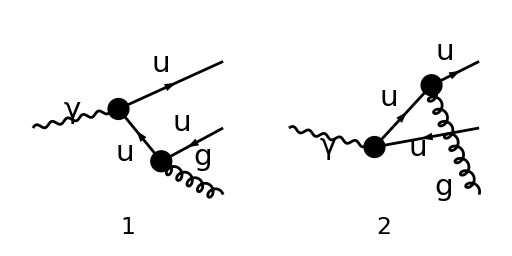

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
diags=InsertFields[CreateTopologies[0,1->3],{V[1]}->{F[3,{1}],-F[3,{1}],V[5]},InsertionLevel->{Classes},Model->"SMQCD"];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

## Obtain the amplitude

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->False,List->False,SMP->True,Contract->True,DropSumOver->True,Prefactor->3/2 SMP["e_Q"],FinalSubstitutions->{SMP["m_u"]->SMP["m_q"]}]
```

(e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1],m_q)).(γ̄·(ε̄)^*(k_3)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(p)).(φ(-OverBar[k_2],m_q)))/((-OverBar[k_1]-OverBar[k_3])^2-m_q^2)+(e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1],m_q)).(γ̄·ε̄(p)).(γ̄·(-OverBar[k_2]-OverBar[k_3])+m_q).(γ̄·(ε̄)^*(k_3)).(φ(-OverBar[k_2],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2)

```mathematica
masslessamp[0] = amp[0]/.{SMP["m_q"]:>0}
```

(e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1])).(γ̄·(ε̄)^*(k_3)).(γ̄·(OverBar[k_1]+OverBar[k_3])).(γ̄·ε̄(p)).(φ(-OverBar[k_2])))/(-OverBar[k_1]-OverBar[k_3])^2+(e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1])).(γ̄·ε̄(p)).(γ̄·(-OverBar[k_2]-OverBar[k_3])).(γ̄·(ε̄)^*(k_3)).(φ(-OverBar[k_2])))/(OverBar[k_2]+OverBar[k_3])^2

## Fix the kinematics

```mathematica
FCClearScalarProducts[];
ScalarProduct[k1]=SMP["m_q"]^2;
ScalarProduct[k2]=SMP["m_q"]^2;
ScalarProduct[k3]=0;
ScalarProduct[k1,k2]=QQ/2 (1-x3);
ScalarProduct[k1,k3]=QQ/2 (1-x2);
ScalarProduct[k2,k3]=QQ/2 (1-x1);
```

Test momentum conservation:

```mathematica
SP[k1+k2+k3]//ScalarProductExpand//Expand
```

2 m_q^2-QQ x1-QQ x2-QQ x3+3 QQ

```mathematica
EMtest=SP[k1+k2+k3]//ScalarProductExpand//Expand
```

2 m_q^2-QQ x1-QQ x2-QQ x3+3 QQ

```mathematica
EMtest/.{SMP["m_q"]:>0,x3->2-x1-x2}//Simplify
```

QQ

## Compute the squared amplitude

All at once!

```mathematica
ampSquared[0]=(amp[0] (ComplexConjugate[amp[0]]))//SUNSimplify//DoPolarizationSums[#,p,0,VirtualBoson->True]&//DoPolarizationSums[#,k3,0,VirtualBoson->True]&//FermionSpinSum//DiracSimplify//FeynAmpDenominatorExplicit//Simplify
```

1/(QQ^2 (x1-1)^2 (x2-1)^2)8 e^2 C_A C_F e_Q^2 g_s^2 (2 QQ m_q^2 (x1^3+x1^2 (x2+x3-5)+x1 (x2^2-4 x2 x3+2 x3+4)+x2^3+x2^2 (x3-5)+2 x2 (x3+2)-2 (x3+1))-8 m_q^4 (x1^2-2 x1+x2^2-2 x2+2)+QQ^2 (x1-1) (x2-1) (x1^2+2 x1 (x3-2)+x2^2+2 x2 (x3-2)+2 (x3-2)^2))

```mathematica
ampSquaredMassless[0]=ampSquared[0]//ReplaceAll[#,{SMP["m_q"]->0,x3->2-x1-x2,SMP["e"]^2->(4 Pi SMP["alpha_fs"]),SMP["g_s"]^2->(4 Pi SMP["alpha_s"])}]&//Simplify//SUNSimplify[#,SUNNToCACF->False]&
```

(64 π^2 α (N^2-1) e_Q^2 α_s (x1^2+x2^2))/((x1-1) (x2-1))

```mathematica
ampSquaredMasslessSUNN3[0]=ampSquaredMassless[0]/. SUNN->3
```

(512 π^2 α e_Q^2 α_s (x1^2+x2^2))/((x1-1) (x2-1))

Now let’s break it down into steps:

### Squaring

```mathematica
amp[0]
```

(e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1],m_q)).(γ̄·(ε̄)^*(k_3)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(p)).(φ(-OverBar[k_2],m_q)))/((-OverBar[k_1]-OverBar[k_3])^2-m_q^2)+(e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1],m_q)).(γ̄·ε̄(p)).(γ̄·(-OverBar[k_2]-OverBar[k_3])+m_q).(γ̄·(ε̄)^*(k_3)).(φ(-OverBar[k_2],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2)

```mathematica
STEP1=(amp[0] (ComplexConjugate[amp[0]]))
```

((e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1],m_q)).(γ̄·(ε̄)^*(k_3)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(p)).(φ(-OverBar[k_2],m_q)))/((-OverBar[k_1]-OverBar[k_3])^2-m_q^2)+(e e_Q g_s T_Col2Col3^Glu4 (φ(OverBar[k_1],m_q)).(γ̄·ε̄(p)).(γ̄·(-OverBar[k_2]-OverBar[k_3])+m_q).(γ̄·(ε̄)^*(k_3)).(φ(-OverBar[k_2],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2)) ((e e_Q g_s T_Col3Col2^Glu4 (φ(-OverBar[k_2],m_q)).(γ̄·(ε̄)^*(p)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(k_3)).(φ(OverBar[k_1],m_q)))/((OverBar[k_1]+OverBar[k_3])^2-m_q^2)+(e e_Q g_s T_Col3Col2^Glu4 (φ(-OverBar[k_2],m_q)).(γ̄·ε̄(k_3)).(γ̄·(-OverBar[k_2]-OverBar[k_3])+m_q).(γ̄·(ε̄)^*(p)).(φ(OverBar[k_1],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2))

### Color Simplify

Simplifying the color, appearing in the expanded term

```mathematica
(STEP1//Expand)⟦1⟧
```

(e^2 e_Q^2 g_s^2 T_Col2Col3^Glu4 T_Col3Col2^Glu4 (φ(OverBar[k_1],m_q)).(γ̄·(ε̄)^*(k_3)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(p)).(φ(-OverBar[k_2],m_q)) (φ(-OverBar[k_2],m_q)).(γ̄·(ε̄)^*(p)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(k_3)).(φ(OverBar[k_1],m_q)))/(((-OverBar[k_1]-OverBar[k_3])^2-m_q^2) ((OverBar[k_1]+OverBar[k_3])^2-m_q^2))

```mathematica
SUNTF[a,i,j]SUNTF[a,j,i]
```

T_ij^a T_ji^a

```mathematica
SUNSimplify[SUNTF[a,i,j]SUNTF[a,j,i]]
SUNSimplify[SUNTF[a,i,j]SUNTF[a,j,i], SUNNToCACF->False]
```

C_A C_F

1/2 (N^2-1)

```mathematica
STEP2=SUNSimplify[STEP1, SUNNToCACF->False]
```

1/2 e^2 (N^2-1) e_Q^2 g_s^2 (((φ(OverBar[k_1],m_q)).(γ̄·(ε̄)^*(k_3)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(p)).(φ(-OverBar[k_2],m_q)))/((OverBar[k_1]+OverBar[k_3])^2-m_q^2)+((φ(OverBar[k_1],m_q)).(γ̄·ε̄(p)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄·(ε̄)^*(k_3)).(φ(-OverBar[k_2],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2)) (((φ(-OverBar[k_2],m_q)).(γ̄·(ε̄)^*(p)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(k_3)).(φ(OverBar[k_1],m_q)))/((OverBar[k_1]+OverBar[k_3])^2-m_q^2)+((φ(-OverBar[k_2],m_q)).(γ̄·ε̄(k_3)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄·(ε̄)^*(p)).(φ(OverBar[k_1],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2))

### Polarization sums

```mathematica
DiracGamma[Momentum[Polarization[p,ⅈ]]]DiracGamma[Momentum[Polarization[p,-ⅈ]]]
DoPolarizationSums[%,p,0,VirtualBoson->True]
```

γ̄·(ε̄)^*(p) γ̄·ε̄(p)

-((γ̄)^($MU($155)))^2

```mathematica
Spinor[Momentum[k1],0,1].ComplexConjugate[Spinor[Momentum[k1],0,1]]
FermionSpinSum[%]
```

(φ(OverBar[k_1])).(φ(OverBar[k_1]))

tr(γ̄·OverBar[k_1])

```mathematica
STEP2
```

1/2 e^2 (N^2-1) e_Q^2 g_s^2 (((φ(OverBar[k_1],m_q)).(γ̄·(ε̄)^*(k_3)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(p)).(φ(-OverBar[k_2],m_q)))/((OverBar[k_1]+OverBar[k_3])^2-m_q^2)+((φ(OverBar[k_1],m_q)).(γ̄·ε̄(p)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄·(ε̄)^*(k_3)).(φ(-OverBar[k_2],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2)) (((φ(-OverBar[k_2],m_q)).(γ̄·(ε̄)^*(p)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄·ε̄(k_3)).(φ(OverBar[k_1],m_q)))/((OverBar[k_1]+OverBar[k_3])^2-m_q^2)+((φ(-OverBar[k_2],m_q)).(γ̄·ε̄(k_3)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄·(ε̄)^*(p)).(φ(OverBar[k_1],m_q)))/((OverBar[k_2]+OverBar[k_3])^2-m_q^2))

```mathematica
STEP3=(STEP2
//DoPolarizationSums[#,p,0,VirtualBoson->True]&
//DoPolarizationSums[#,k3,0,VirtualBoson->True]&
//FermionSpinSum
)
```

1/2 e^2 (N-1) (N+1) e_Q^2 g_s^2 (1/((OverBar[k_1]+OverBar[k_3])^2-m_q^2))^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($291)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($289)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($289)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($291)))+1/2 e^2 (N-1) (N+1) e_Q^2 g_s^2 (1/((OverBar[k_2]+OverBar[k_3])^2-m_q^2))^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($289)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($291)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($291)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($289)))+(e^2 (N-1) (N+1) e_Q^2 g_s^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($289)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($291)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($289)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($291))))/(2 ((OverBar[k_1]+OverBar[k_3])^2-m_q^2) ((OverBar[k_2]+OverBar[k_3])^2-m_q^2))+(e^2 (N-1) (N+1) e_Q^2 g_s^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($291)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($289)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($291)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($289))))/(2 ((OverBar[k_1]+OverBar[k_3])^2-m_q^2) ((OverBar[k_2]+OverBar[k_3])^2-m_q^2))

### Gamma Algebra

```mathematica
STEP3
```

1/2 e^2 (N-1) (N+1) e_Q^2 g_s^2 (1/((OverBar[k_1]+OverBar[k_3])^2-m_q^2))^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($291)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($289)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($289)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($291)))+1/2 e^2 (N-1) (N+1) e_Q^2 g_s^2 (1/((OverBar[k_2]+OverBar[k_3])^2-m_q^2))^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($289)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($291)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($291)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($289)))+(e^2 (N-1) (N+1) e_Q^2 g_s^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($289)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($291)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($289)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($291))))/(2 ((OverBar[k_1]+OverBar[k_3])^2-m_q^2) ((OverBar[k_2]+OverBar[k_3])^2-m_q^2))+(e^2 (N-1) (N+1) e_Q^2 g_s^2 tr((γ̄·OverBar[k_1]+m_q).(γ̄)^($MU($291)).(γ̄·(OverBar[k_1]+OverBar[k_3])+m_q).(γ̄)^($MU($289)).(γ̄·OverBar[k_2]-m_q).(γ̄)^($MU($291)).(m_q-γ̄·(OverBar[k_2]+OverBar[k_3])).(γ̄)^($MU($289))))/(2 ((OverBar[k_1]+OverBar[k_3])^2-m_q^2) ((OverBar[k_2]+OverBar[k_3])^2-m_q^2))

```mathematica
DiracTrace[
DiracGamma[LorentzIndex[μ1]].DiracGamma[LorentzIndex[ν1]].DiracGamma[LorentzIndex[ρ1]].DiracGamma[LorentzIndex[σ1]]
]DiracTrace[
DiracGamma[LorentzIndex[μ1]].DiracGamma[LorentzIndex[ν1]].DiracGamma[LorentzIndex[ρ1]].DiracGamma[LorentzIndex[σ1]]
]
DiracSimplify[%]
```

(tr((γ̄)^μ1.(γ̄)^ν1.(γ̄)^ρ1.(γ̄)^σ1))^2

640

```mathematica
DiracTrace[
DiracGamma[LorentzIndex[μ,d],d].DiracGamma[LorentzIndex[μ,d],d]
]
DiracSimplify[%]
```

tr(γ^μ.γ^μ)

4 d

```mathematica
STEP4=DiracSimplify[STEP3]//Simplify
```

4 e^2 (N^2-1) e_Q^2 g_s^2 ((2 QQ m_q^2 (x1+2 x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1)) (1/((OverBar[k_1]+OverBar[k_3])^2-m_q^2))^2+(2 QQ m_q^2 (2 x1+x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1)) (1/((OverBar[k_2]+OverBar[k_3])^2-m_q^2))^2+(2 QQ (QQ (x3-1) (x1+x2+x3-3)-m_q^2 (x1+x2+4 x3-6)))/(((OverBar[k_1]+OverBar[k_3])^2-m_q^2) ((OverBar[k_2]+OverBar[k_3])^2-m_q^2)))

### Combine it all with the explicit kinematic parameterisation

```mathematica
STEP5 = STEP4//FeynAmpDenominatorExplicit
```

4 e^2 (N^2-1) e_Q^2 g_s^2 ((2 QQ m_q^2 (2 x1+x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1))/(QQ-QQ x1)^2+(2 QQ m_q^2 (x1+2 x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1))/(QQ-QQ x2)^2+(2 QQ (QQ (x3-1) (x1+x2+x3-3)-m_q^2 (x1+x2+4 x3-6)))/((QQ-QQ x1) (QQ-QQ x2)))

```mathematica
RealEmissionMassive=STEP5//FullSimplify
```

4 e^2 (N^2-1) e_Q^2 g_s^2 ((2 QQ m_q^2 (2 x1+x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1))/(QQ-QQ x1)^2+(2 QQ m_q^2 (x1+2 x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1))/(QQ-QQ x2)^2+(2 QQ (x3-1) (x1+x2+x3-3)-2 m_q^2 (x1+x2+4 x3-6))/(QQ (x1-1) (x2-1)))

```mathematica
RealEmissionMassless= RealEmissionMassive/.{SMP["m_q"]->0,x3->2-x1-x2}
```

4 e^2 (N^2-1) e_Q^2 g_s^2 ((QQ^2 (x1-1) (x2-1))/(QQ-QQ x1)^2+(QQ^2 (x1-1) (x2-1))/(QQ-QQ x2)^2-(2 (-x1-x2+1))/((x1-1) (x2-1)))

Clean up couplings and set N_c=3!

```mathematica
RealEmissionMassive=RealEmissionMassive /. {SUNN -> 3, SMP["e"]^2 -> (4 Pi SMP["alpha_fs"]), SMP["g_s"]^2 -> (4 Pi SMP["alpha_s"])} // FullSimplify
```

512 π^2 α e_Q^2 α_s ((2 QQ m_q^2 (2 x1+x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1))/(QQ-QQ x1)^2+(2 QQ m_q^2 (x1+2 x2+x3-4)-8 m_q^4+QQ^2 (x1-1) (x2-1))/(QQ-QQ x2)^2+(2 QQ (x3-1) (x1+x2+x3-3)-2 m_q^2 (x1+x2+4 x3-6))/(QQ (x1-1) (x2-1)))

```mathematica
RealEmissionMassless=RealEmissionMassless /. {SUNN -> 3, SMP["e"]^2 -> (4 Pi SMP["alpha_fs"]), SMP["g_s"]^2 -> (4 Pi SMP["alpha_s"])} // FullSimplify
```

(512 π^2 α e_Q^2 α_s (x1^2+x2^2))/((x1-1) (x2-1))

### D-dimensional

Or wrapped through a function:

```mathematica
ComputeDiags[diags_, dim_]:=Module[{fcamp,ampsq},
fcamp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->dim,List->False,SMP->True,Contract->True,DropSumOver->True,Prefactor->3/2 SMP["e_Q"],FinalSubstitutions->{SMP["m_u"]->SMP["m_q"]}];
FCClearScalarProducts[];
ScalarProduct[k1]=SMP["m_q"]^2;
ScalarProduct[k2]=SMP["m_q"]^2;
ScalarProduct[k3]=0;
ScalarProduct[k1,k2]=QQ/2 (1-x3);
ScalarProduct[k1,k3]=QQ/2 (1-x2);
ScalarProduct[k2,k3]=QQ/2 (1-x1);
ampsq=(fcamp (ComplexConjugate[fcamp]))//SUNSimplify//DoPolarizationSums[#,p,0,VirtualBoson->True]&//DoPolarizationSums[#,k3,0,VirtualBoson->True]&//FermionSpinSum//DiracSimplify//FeynAmpDenominatorExplicit//Simplify;
ampsq//ReplaceAll[#,{SMP["m_q"]->0,x3->2-x1-x2,SMP["e"]^2->(4 Pi SMP["alpha_fs"]),SMP["g_s"]^2->(4 Pi SMP["alpha_s"]),SUNN->3}]&//Simplify//SUNSimplify[#,SUNNToCACF->False]&
]
```

```mathematica
diags=InsertFields[CreateTopologies[0,1->3],{V[1]}->{F[3,{1}],-F[3,{1}],V[5]},InsertionLevel->{Classes},Model->"SMQCD"];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
RealEmissionMasslessDdimensional=(* Correct D-dimension photon spin averaging *)(2/(2-2ϵ)ComputeDiags[diags,D])/.{D->4-2ϵ}//Series[#,{ϵ,0,1}]&//Normal//FullSimplify
```

-Graphics-

(64 π^2 α (N^2-1) e_Q^2 α_s (x1^2-ϵ (x1+x2-2)^2+x2^2))/((x1-1) (x2-1))

```mathematica
(
64 π^2 SMP["alpha_fs"]SMP["alpha_s"](SUNN^2 - 1) SMP["e_Q"]^2(((1-ϵ)(x1^2+x2^2)+2ϵ(1-x3))/((1-x1)(1-x2))-2ϵ)
-RealEmissionMasslessDdimensional
)/.{x3->2-x1-x2,SUNN->3}//FullSimplify
```

0

## Compute the Born

```mathematica
diags=InsertFields[CreateTopologies[0,1->2],{V[1]}->{F[3,{1}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD"];
fcamp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,Contract->True,DropSumOver->True,Prefactor->3/2 SMP["e_Q"],FinalSubstitutions->{SMP["m_u"]->SMP["m_q"]}];
FCClearScalarProducts[];
ScalarProduct[k1]=SMP["m_q"]^2;
ScalarProduct[k2]=SMP["m_q"]^2;
ScalarProduct[k1,k2]=QQ/2 ;
ampsq=(fcamp (ComplexConjugate[fcamp]))//SUNSimplify[#,SUNNToCACF->False]&//DoPolarizationSums[#,p,0,VirtualBoson->True]&//FermionSpinSum//DiracSimplify//FeynAmpDenominatorExplicit//Simplify;
ampsq//ReplaceAll[#,{SMP["m_q"]->0,x3->2-x1-x2,SMP["e"]^2->(4 Pi SMP["alpha_fs"]),SMP["g_s"]^2->(4 Pi SMP["alpha_s"])}]&//Simplify;
BornMassless=ampsq/.{SMP["m_q"]->0,SUNN->3,SMP["e"]^2 -> (4 Pi SMP["alpha_fs"]),D->4-2ϵ}
```

24 π α QQ (2-2 ϵ) e_Q^2